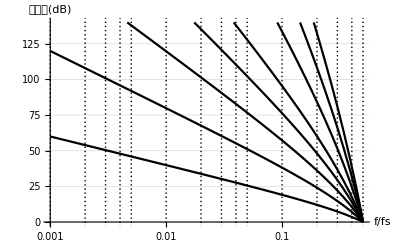

```mathematica
Gratfil[f_,fs_,order_]:=((fs-f)/f)^order;
LogLinearPlot[20*Log10[Gratfil[f,1,{1,2,3,4,5,7,9,11}]],{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.001,0.5+0.00001},{0,140}},GridLines->{{0.001,0.002,0.003,0.004,0.005,0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["信镜比(dB)",FontFamily->"Times",FontSize->12]}]
```